## Introduction

Code to simulate forced swarmalators on a ring. The colored dots in the graphics are the order parameters:

Y=1/N Σ ⅇ^(ⅈ x)
Z = 1/N Σ ⅇ^(ⅈ θ)
W_±=1/N Σ ⅇ^(ⅈ (x ±θ))

#### Notes:

1. Don’t forget J = -1 --> something interesting here?
2.

## Main

### Dynamic simulations

$Aborted

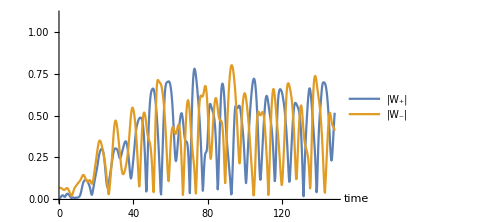
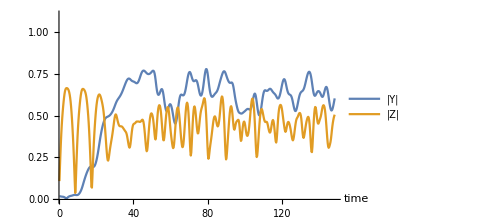
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.25,500,300}; 
{J,k,f,Δ}={1,-0.5,0.7,1}; 
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{ts,Wps,Wms,Ys,Zs}={{},{},{},{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
results=plotResults[znew];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1.1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1.1}];
Grid[{{p1,p2}}]
```

### Static simulation

#### Simulation

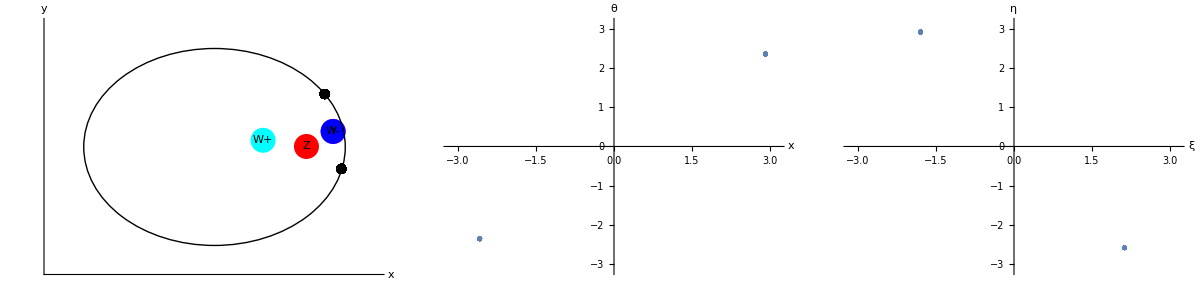

```mathematica
(*Preample*)
{dt,n,T}={0.25,200,500}; 
{J,k,f,Δ}={1,-3,1.5,0}; 
{z0,znew}={Table[RandomReal[{0,0.1π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
```

```mathematica
{x,θ}=znew;
```

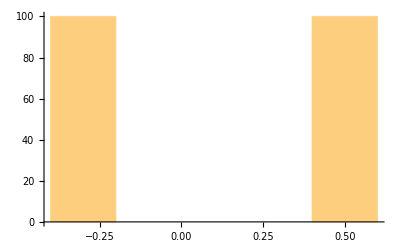

```mathematica
Histogram[x]
```

#### Plots

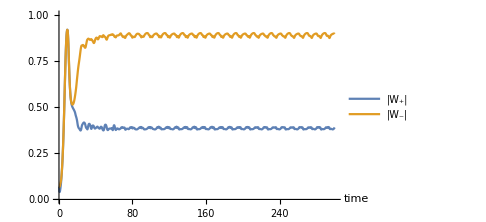
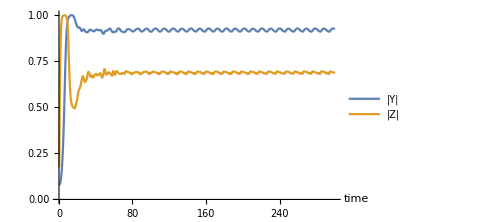
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

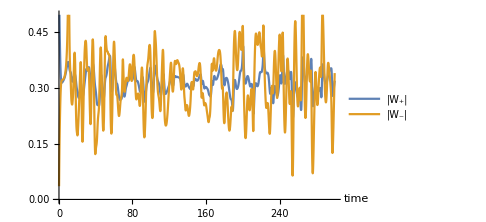
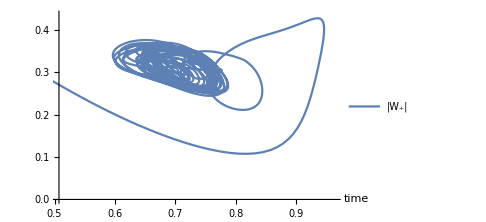
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{{ts,Wps//Arg}ᵀ,{ts,Wms//Arg}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium];
p2=ListPlot[{Wps//Abs,Wms//Abs}ᵀ,AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium];
Grid[{{p1,p2}}]
```

```mathematica
Manipulate[ListPlot[{xs[[t,All]]//mod,θs[[t,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}],{t,1,Dimensions[xs][[2]],1}]
```

Part::partd: Part specification xs⟦105,All⟧ is longer than depth of object.

Part::partd: Part specification θs⟦105,All⟧ is longer than depth of object.

Part::partd: Part specification xs⟦105,All⟧ is longer than depth of object.

Part::partd: Part specification θs⟦105,All⟧ is longer than depth of object.

## Catalog states

1. There are fixed points we can perturb around.
2. But the dynamical states are non-steady -- order parameters oscillate. So hard to analyze these. Hmm.
3. Is the static phase wave stable?
4. Is the static async stable? 
5. I suspect we see chaos.

### Pinned state (should be able to calculate F_crit) -- done

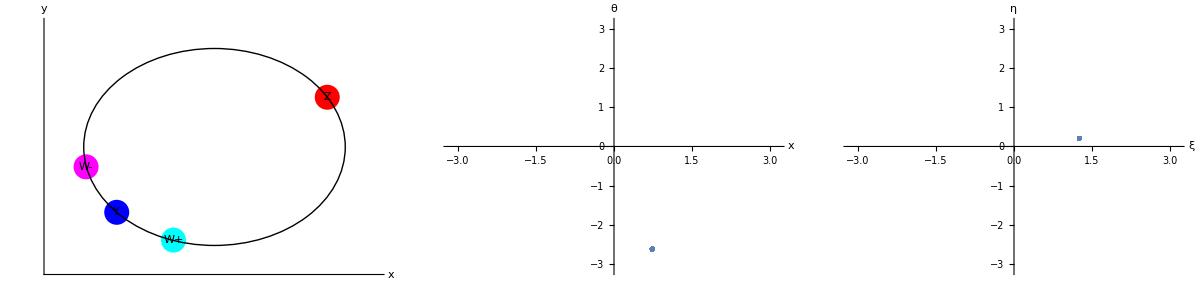

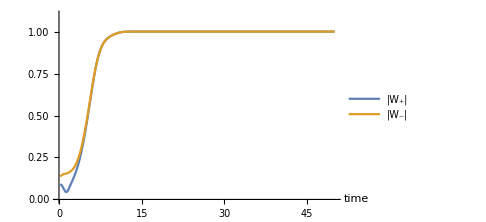
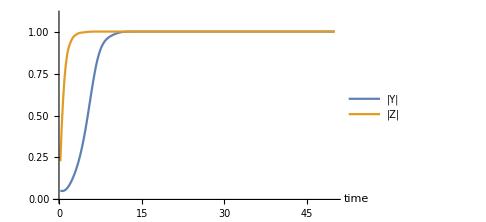
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,200,50}; 
{J,k,f,Δ}={1,1,2,1};  
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]

p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1.1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1.1}];
Grid[{{p1,p2}}]
```

### Static wobble

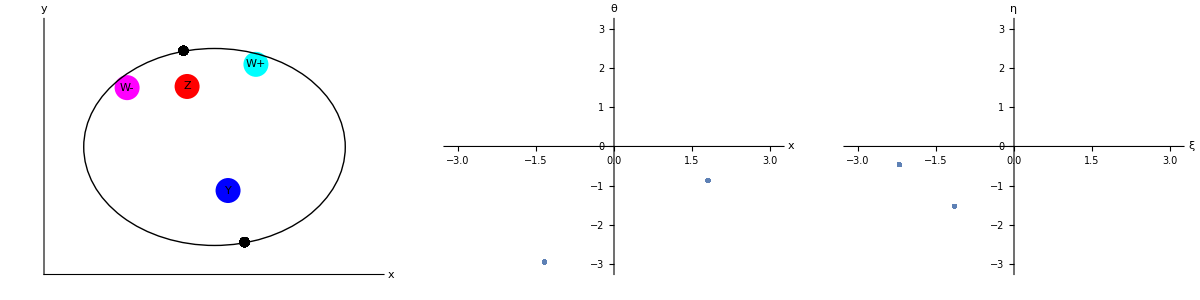

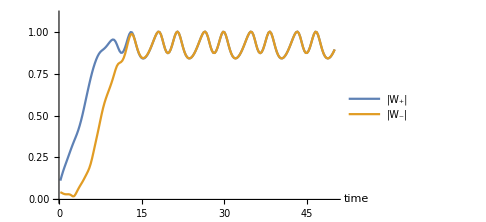
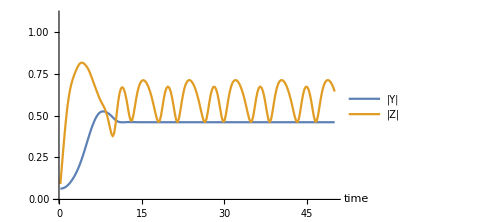
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,200,50}; 
{J,k,f,Δ}={1,1,0.85,1};  
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]

p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1.1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1.1}];
Grid[{{p1,p2}}]
```

### Breathing phase wave -- like vinegar eels?

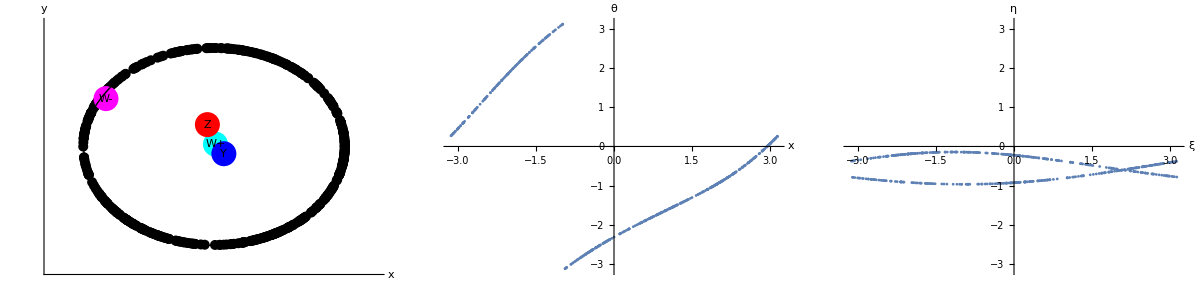

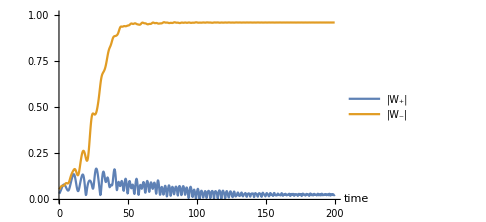
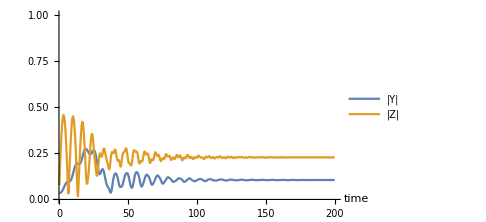
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,500,200}; 
{J,k,f,Δ}={1,-0.5,0.4,1};  
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

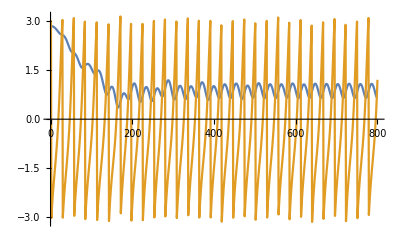

```mathematica
ListPlot[{xs[[All,1]],θs[[All,1]]//mod},Joined->True]
```

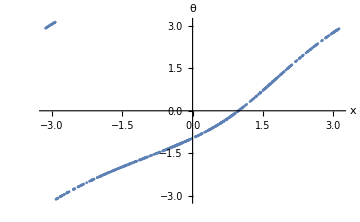
-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{xs[[-20,All]]//mod,θs[[-20,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=Grid[{{p2,p1}}]
Export["figures/breathing-phase-wave.png",p3];
```

### Erratic phase wave (large breathing)

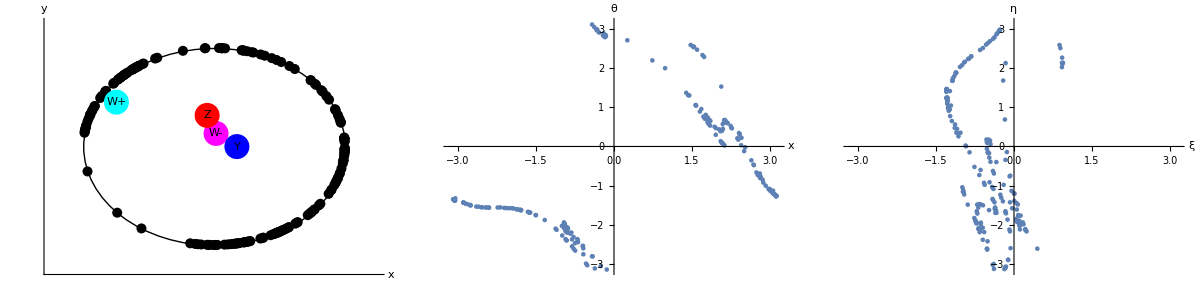

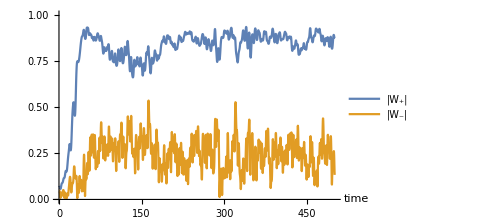
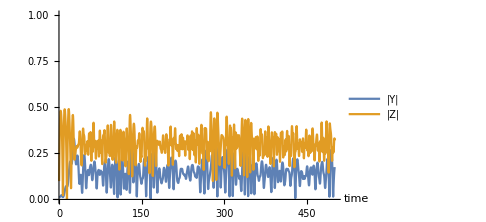
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,200,500}; 
{J,k,f,Δ}={1,-0.5,0.5,1};  
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Static sync (K = -0.5, F = 2)

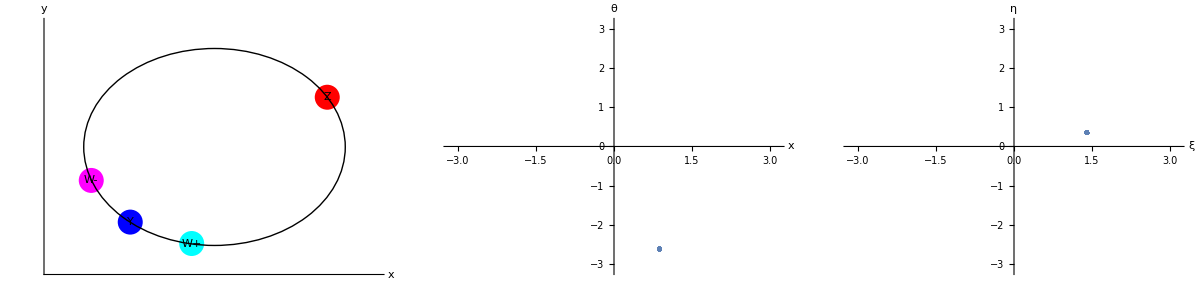

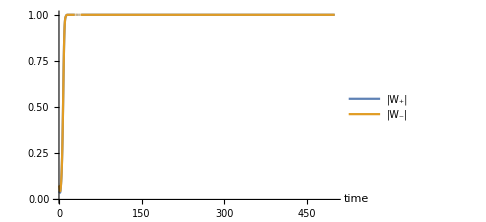
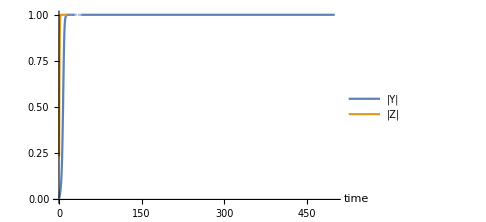
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,200,500}; 
{J,k,f,Δ}={1,-0.5,2,1};  
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Static incoherence (K = -0.5, F = 1)

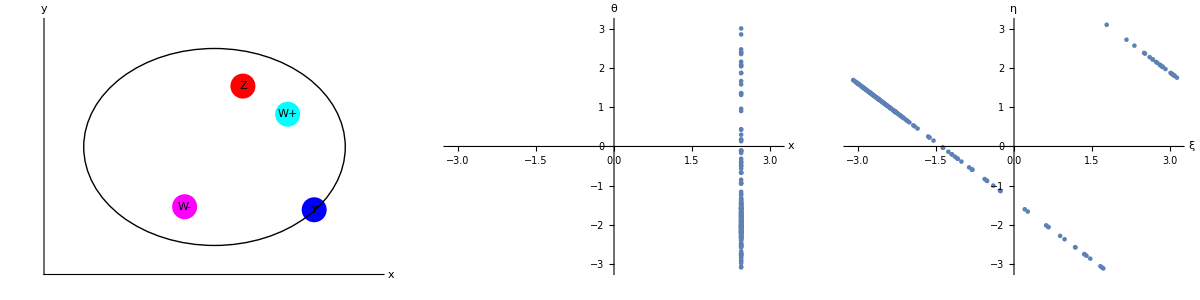

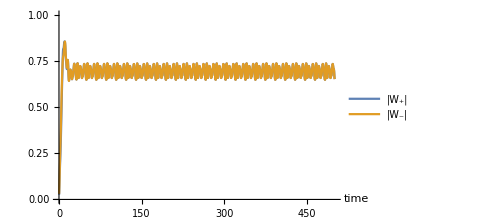
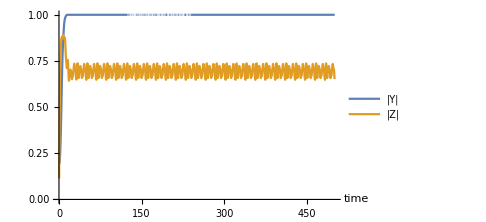
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,200,500}; 
{J,k,f,Δ}={1,-0.5,1,1};  
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Unsteady incoherence (K = -2, F = 1)

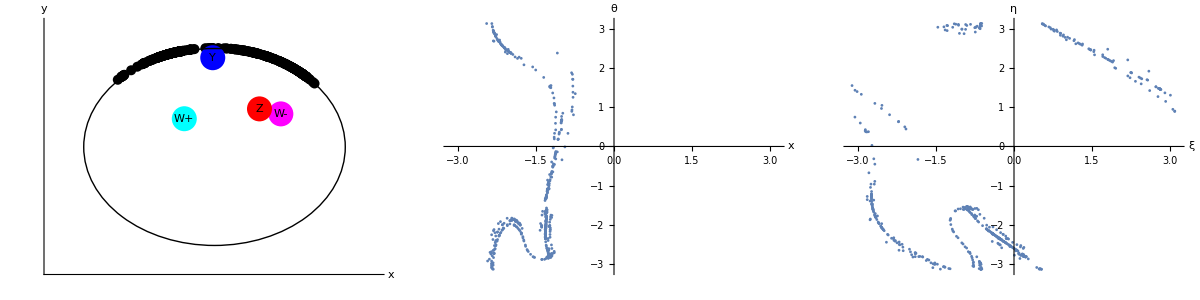

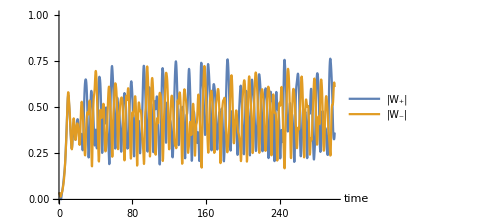
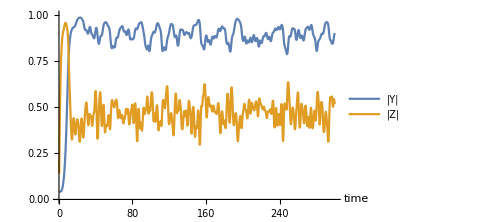
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,500,300}; 
{J,k,f,Δ}={1,-2,1,1};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Split state (fixed point) for Δ = 0. Chaos here? Thorough study

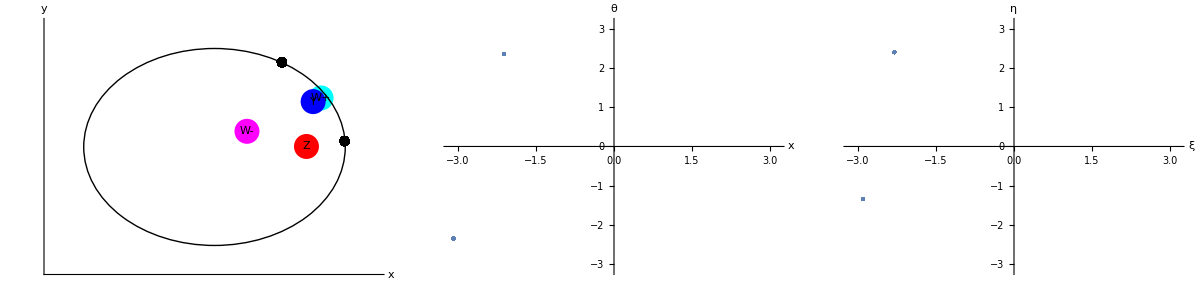

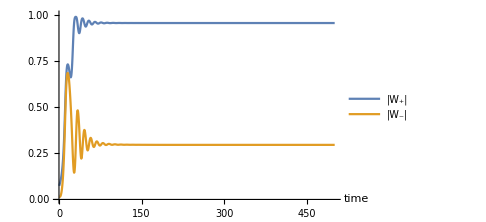
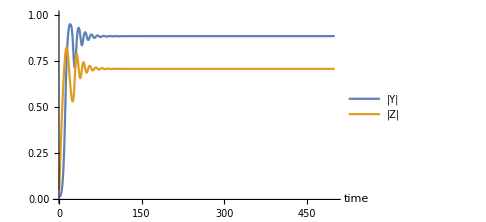
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,500,500}; 
{J,k,f,Δ}={1,-0.5,0.2,0}; 

{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Chaos?

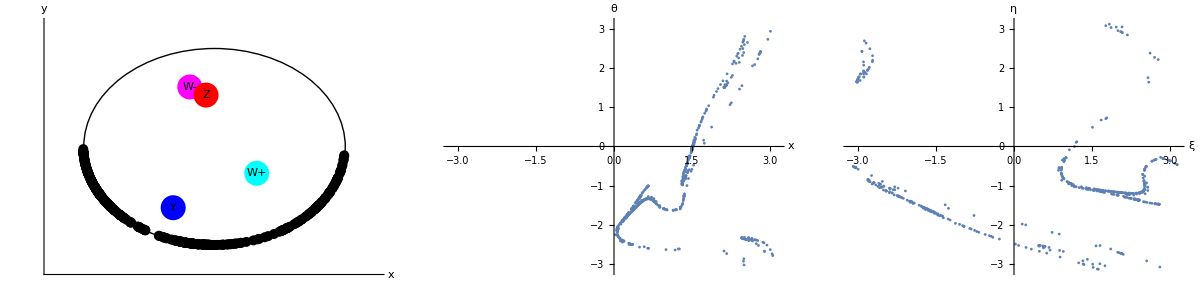

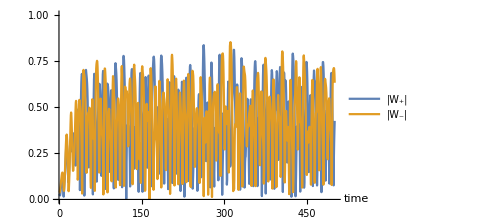
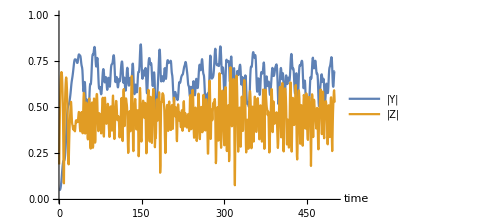
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,500,500}; 
{J,k,f,Δ}={1,-0.5,0.7,1}; 

{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Talking two cluster state

Like the 2D. Splintered phase wave.

#### Regular

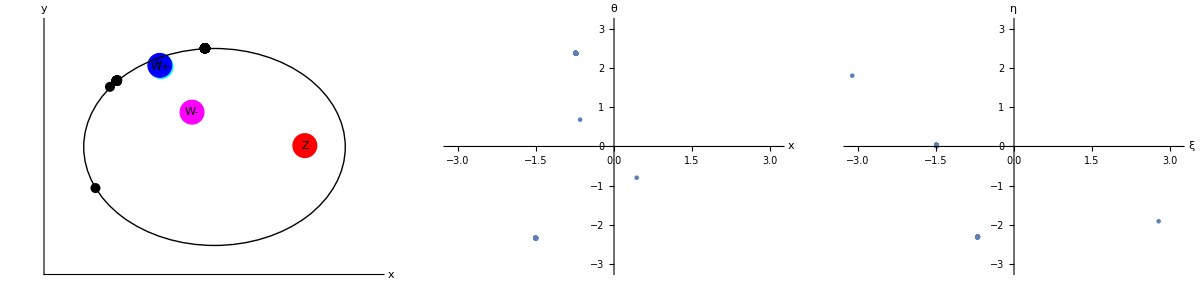

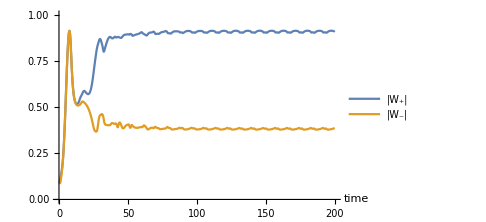
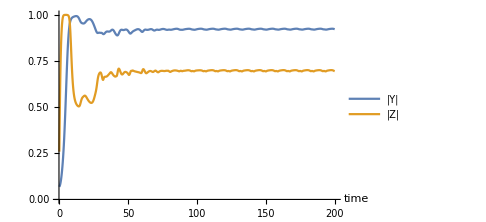
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,200,200}; 
{J,k,f,Δ}={1,-3,1.5,0}; 
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### Setting the initial condition narrow enough kills the number of drifters.

1. Should be able to calculate stability of this one
2. x_1 = 0, x_2=? θ_1=θ_2+π/2. Two populations: (x_1,θ_1) and (x_2,θ_2)=(x_1+C(parameters), θ_1+π/2)

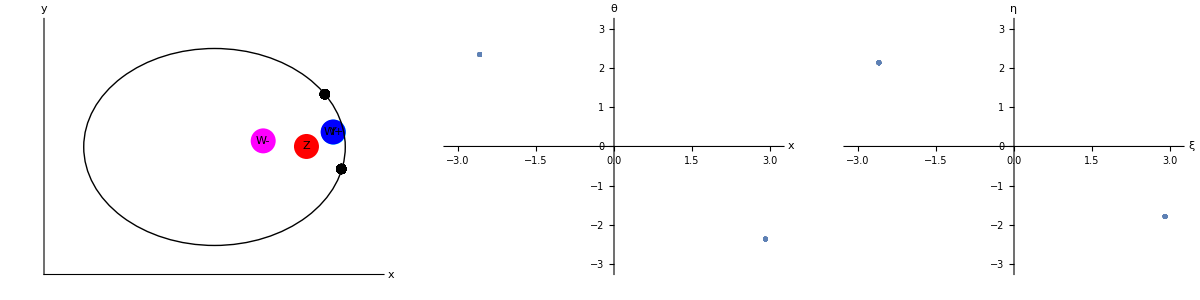

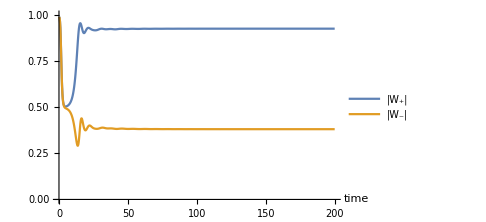
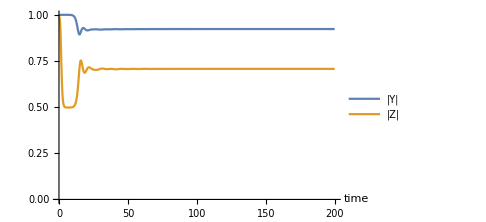
-Graphics- | -Graphics-

```mathematica
(*Preample*)
{dt,n,T}={0.25,200,200}; 
{J,k,f,Δ}={1,-3,1.5,0}; 
{z0,znew}={Table[RandomReal[{0,0.1π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs,ts}={{},{},{}};
{Wps,Wms,Ys,Zs}={{},{},{},{}};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,f,Δ];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Y,Z,Wp,Wm}=findOrderPars[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Ys,Y];AppendTo[Zs,Z];
];

plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Ys//Abs}ᵀ,{ts,Zs//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|Y|","|Z|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

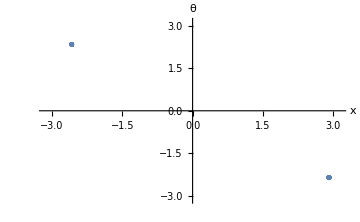
-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"|W_+|","|W_-|"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{xs[[-20,All]]//mod,θs[[-20,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=Grid[{{p2,p1}}]
Export["figures/two-cluster-state.png",p3];
```

## Bif diagram

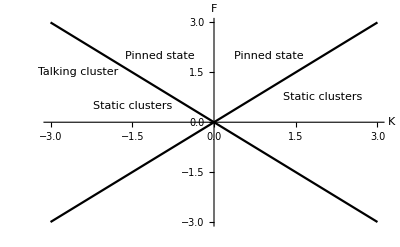

```mathematica
Plot[{k,-k},{k,-3,3},PlotStyle->Black,AxesLabel->{Style["K",15,Italic],Style["F",15,Italic]},
Epilog->{
Text["Pinned state",{1.0,2}],
Text["Pinned state",{-1,2}],
Text["Talking cluster",{-2.5,1.5}],
Text["Static clusters",{-1.5,0.5}],
Text["Static clusters",{2.0,0.75}]
}]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real},{F,_Real},{Δ,_Real}},
Module[{i,j,xji,yji,thetaji,thetai,thetaj,xi,xj,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,vel=ConstantArray[0.0,{2,n}]},
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetai=z[[2,i]];
thetaj=z[[2,j]];
xi=z[[1,i]];
xj=z[[1,j]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji] Cos[thetaji];
thetatemp=k*Sin[thetaji] Cos[xji] ;
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=Δ-F Sin[thetai]+thetatemp;vel[[2,j]]+=Δ-F Sin[thetaj]-thetatemp;
];
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];


findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
];


findOrderPars[z_]:=Block[{Z,Y,Wp,Wm,i,numOsc,x,theta,},
{Z,Y,Wp,Wm}={0,0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
{x,theta}={z[[1,i]],z[[2,i]]};
Y+=Exp[ⅈ x];Z+=Exp[ⅈ theta];
Wp+=Exp[ⅈ (x+theta)];
Wm+=Exp[ⅈ (x-theta)];
];
Return[{Y/numOsc,Z/numOsc,Wp/numOsc,Wm/numOsc}]
];


plotResults[z_]:=Block[{colors,Y,Z,Wp,Wm,p1,p2,p3,x,θ},
{x,θ}={z[[1,All]],z[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Y,Z,Wp,Wm}=findOrderPars[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Blue,Point[{Y//Re,Y//Im}],Black,Text["Y",{Y//Re,Y//Im}],
Red,Point[{Z//Re,Z//Im}],Black,Text["Z",{Z//Re,Z//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

Return[Grid[{{p1,p2,p3}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,f_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,f];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,f_,Δ_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,f,Δ];
k2=F[z+dt/2 k1,n,J,k,f,Δ];
k3=F[z+dt/2 k2,n,J,k,f,Δ];
k4=F[z+dt k3,n,J,k,f,Δ];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];
```